#### Define needed operators and constants

```mathematica
integration$bounds = {l-> 0.25, rmax-> 20};
ℤ=({{1, 0}, {0, -1}}); (*sigma z*)
ρ [θρ_,ϕρ_]=({{(Cos[θρ/2])^2, Cos[θρ/2]*Sin[θρ/2]*Exp[-ⅈ*ϕρ]}, {Cos[θρ/2]*Sin[θρ/2]*Exp[ⅈ*ϕρ], (Sin[θρ/2])^2}}); (*Density matrix*)
I$up=1/2(({{1, 0}, {0, 1}})+1*ℤ); (*Pi_i=Z with eigenvalue 1*)
I$down=1/2(({{1, 0}, {0, 1}})-1*ℤ);(*Pi_i=Z with eigenvalue -1*)
A[θa_, ϕa_]=({{Cos[θa], Sin[θa]*Cos[ϕa]-ⅈ*Sin[θa]*Sin[ϕa]}, {Sin[θa]*Cos[ϕa]+ⅈ*Sin[θa]*Sin[ϕa], -Cos[θa]}});
F[θf_,ϕf_]=({{Cos[θf], Sin[θf]*Cos[ϕf]-ⅈ*Sin[θf]*Sin[ϕf]}, {Sin[θf]*Cos[ϕf]+ⅈ*Sin[θf]*Sin[ϕf], -Cos[θf]}});
𝕄$ra[r_,θa_,ϕa_]=(√l)/(√1)*(δt/(2π*τ))^(1/4)*MatrixExp[-δt/(4*τ) (MatrixPower[r/1({{1, 0}, {0, 1}})-A[θa,ϕa],2])]/.{δt-> 0.1, τ-> 1};
𝕄$ra$dag[r_,θa_,ϕa_]=(√l)/(√1)*(δt/(2π*τ))^(1/4)*MatrixExp[-δt/(4*τ) (MatrixPower[-r/1({{1, 0}, {0, 1}})-A[θa,ϕa],2])]/.{δt-> 0.1, τ-> 1};
F$up[θf_,ϕf_]=1/2(({{1, 0}, {0, 1}})+F[θf,ϕf]); (*Pi_F with eigenvalue 1*)
F$down[θf_,ϕf_]=1/2(({{1, 0}, {0, 1}})-F[θf,ϕf]);(*Pi_F with eigenvalue -1*)
```

Now define probabilities and entropy definitions

```mathematica
p$af$up[r_,θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_] = Tr[F$up[θf,ϕf].𝕄$ra[r,θa,ϕa].ρ[θρ,ϕρ].𝕄$ra$dag[r,θa,ϕa]];
p$af$down[r_,θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_] = Tr[F$down[θf,ϕf].𝕄$ra[r,θa,ϕa].ρ[θρ,ϕρ].𝕄$ra$dag[r,θa,ϕa]];
p$i$up[θρ_,ϕρ_] = Tr[I$up.ρ[θρ,ϕρ]];
p$i$down[θρ_,ϕρ_] = Tr[I$down.ρ[θρ,ϕρ]];
```

```mathematica
H$I[θρ_,ϕρ_]=-p$i$up[θρ,ϕρ] Log[2,p$i$up[θρ,ϕρ]] -p$i$down[θρ,ϕρ] Log[2,p$i$down[θρ,ϕρ]];
H$AF$singleR [r_,θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_] =-p$af$up[r,θρ,ϕρ,θa,θf,ϕf,ϕa]Log[2,p$af$up[r,θρ,ϕρ,θa,θf,ϕf,ϕa]]   -p$af$down[r,θρ,ϕρ,θa,θf,ϕf,ϕa]Log[2,p$af$down[r,θρ,ϕρ,θa,θf,ϕf,ϕa]];
rmax = 20; l=0.25;
H$AF[θρ_,ϕρ_,θa_,θf_,ϕf_,ϕa_] = (Sum[H$AF$singleR[r,θρ,ϕρ,θa,θf,ϕf,ϕa],
{r,-rmax+(l/2),rmax-(l/2),l}]);
```

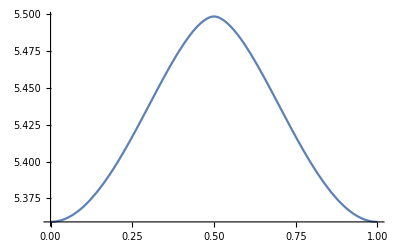
{111.182,-Graphics-}

```mathematica
Plot[(Re[H$AF[x Pi, 0, y Pi,  Pi/2, 0,0]])/.{x-> 0.5}, {y,0,1}]//Timing
```

```mathematica
N[H$AF[Pi/3, 0, 0.1Pi,  Pi/10, 0,0]]//Timing
```

{0.31008,6.02443+0. ⅈ}